## Orbit of Mercury as a Test of General Relativity

In other modules we learn Kepler’s laws, that describe the orbits of planets in our solar system under the influence of the Sun’s gravity.  One of the key equations we encounter is
			
which describes how the inverse radius  evolves as a planet sweeps through an angle  in its orbit around the Sun. This has an analytic solution. Find the analytic solution to this equation with initial conditions at perihelion:
			
			
in terms of the eccentricity  and angular momentum .

```mathematica
ysol = DSolveValue[
{u''[ϕ]+u[ϕ]== G M/L^2, 
u[0]==G M (1+e)/L^2, u'[0]==0}, 
u[ϕ], ϕ]// Simplify
```

(G M (1+e Cos[ϕ]))/L^2

For the most part, Kepler’s laws very accurately describe the orbit of planet planets in our solar system.  However, they do not quite explain the orbit of Mercury. This problem was finally resolved with the advent of Einstein’s theory of General Relativity. When applied to orbits around the Sun, this introduces an extra nonlinear term into the above equation:
			
where  with  the speed of light. This latter equation cannot be easily solved analytically, but we can use perturbation theory (asymptotic expansions) with  as a small parameter. Find the first two terms of the asymptotic expansion of  for small  using initial conditions
			,

```mathematica
eqn=u''[ϕ]+u[ϕ]==(G M/L^2) (1+3 ϵ u[ϕ]^2);

sol=AsymptoticDSolveValue[{eqn,u[0]==G M (1+e)/L^2,u'[0]==0},u[ϕ],ϕ,{ϵ,0,1}]/. ϵ->L^2/c^2 //FullSimplify
```

1/(2 c^2 L^4)G M (2 c^2 L^2+3 (2+e^2) G^2 M^2+2 (c^2 e L^2-(3+e^2) G^2 M^2) Cos[ϕ]+e G^2 M^2 (-e Cos[2 ϕ]+6 ϕ Sin[ϕ]))

A key prediction of General Relativity that differs from Newtonian gravity is that orbits are not closed ellipses, but that they precess, so that perihelion is reached again after one full orbit not at ,  but at . Use your asymptotic solution for  along with the fact that perihelion is the point where the orbital radius reaches a minimum to find an expression for . Hint: You can consider the case where .

```mathematica
RPrime=D[1/sol,ϕ];

shift=SolveValues[Normal[Series[RPrime/. ϕ->2 π+Δϕ,{Δϕ,0,1}]]==0,Δϕ]//FullSimplify
```

{(6 c^2 e (1+e) G^2 L^2 M^2 π)/(c^4 e (1+e) L^4-3 c^2 (1+e)^3 G^2 L^2 M^2+72 e^2 G^4 M^4 π^2)}

By considering the fact that , find the leading order behaviour of your solution for  for large .

```mathematica
reducedshift=Normal[Series[shift,{c,∞, 2}]][[1]]
```

(6 G^2 M^2 π)/(c^2 L^2)

Compute the value of the perihelion precession for the orbit of Mercury about the Sun. Hint: You may find Mathematica’s Quantity["Gravitational Constant"], Quantity["SolarMass"] and Quantity["SpeedOfLight"] useful, and may also use that the angular momentum for Mercury’s orbit is given by:

```mathematica
MercuryL=L->Quantity[2.78 10^15,("Meters")^2/"Seconds"];
```

```mathematica
MercuryG = G->Quantity["GravitationalConstant"];
MercuryM = M->Quantity["SolarMass"];
MercuryC = c->Quantity["SpeedOfLight"];

UnitsReducedShift = reducedshift/.{MercuryL, MercuryG, MercuryM, MercuryC}
```

4.77957×10^-7

The orbital period of Mercury is 88.0 days. Show that over 100 years its orbit will precess by 40.89 seconds of arc.

```mathematica
NumPeriods = 100/88*365;
NumPeriods*UnitsReducedShift*206265 (*radians to seconds of arc*)
```

40.8907

```mathematica
ClearAll;
```

## Matched Asymptotic Expansions

Consider the boundary value problem

Find an exact analytic solution and plot it for several values of

```mathematica
eq = ϵ y''[x]+2y'[x]+2y[x]==0;
ysol = DSolveValue[
{eq, y[0]==0, y[1]==1}, y[x],x
	
] // FullSimplify
```

1/2 ⅇ^(-((-1+x) (1+√(1-2 ϵ)))/ϵ) (-1+ⅇ^((2 x √(1-2 ϵ))/ϵ)) (-1+Coth[(√(1-2 ϵ))/ϵ])

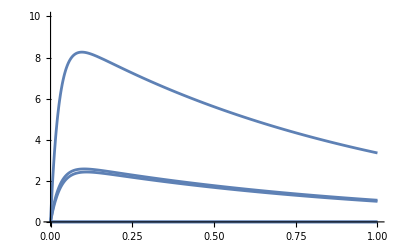

```mathematica
epsilonValues={0.04,0.045,0.05,0.055, 0.06}; (*List of epsilon values*)
plots=Table[Plot[ysol/. ϵ->epsilon,{x,0,1},PlotRange->{{0,1},{0,10}}],{epsilon,epsilonValues}];
Show[plots]
```

Using the method of matched asymptotic expansions, find a composite solution by matching an inner and outer expansion. Explain each step of your calculation.

#### Outer Solution

We define a linear expansion of y(x) in terms of ϵ, with coefficients yc[i].

Expansion is passed back into the ODE and then arranged in terms of ϵ powers.

The term of ϵ of zeroth power is extracted and solved using DSolveValue with the boundary condition ant the boundary layer.

The first power ϵ  is solved similarly however the solution of the zeroth order is substituted in,

A linear combination of each of the solutions  is created with there respective epsilon powers.

```mathematica
ye = Function[x,Sum[yc[i][x]*ϵ^i,{i,0,2}]];
eqe = Collect[eq /. y->ye, ϵ];
y0eq = Coefficient[eqe[[1]], ϵ, 0] == 0;
y0sol = DSolveValue[{y0eq,yc[0][1]==1}, yc[0], x];
y1eq = (Coefficient[eqe[[1]], ϵ, 1] /.yc[0]->y0sol)==0;
y1sol = DSolveValue[{y1eq,yc[1][1]==0}, yc[1],x];
yOut = y0sol[x]+ϵ*y1sol[x]
```

ⅇ^(1-x)-1/2 ⅇ^(1-x) (-1+x) ϵ

#### Inner Solution

The solution is redefined in terms of a new variable Y(X) where X= x/ϵ.

Rescaling is done to convert a singular perturbation problem into a regular perturbation problem.

This rescaling works because we are finding the dominant balance between the terms in the equation.

The differential equation is scaled under the assumption that ϵ ≠ 0.

An asymptotic expansion is passed into the scaled ODE, and organised in terms of ϵ.

The zeroth-order term is solved using DSolveValue and the Coefficient is renamed to maintain.

This is repeated for the first order,  the leading behaviour is then is extracted for by series expansion. The coefficients are solved by setting them equal.

and a linear combination is created again of of both parts of the epsilons

```mathematica
inneq = eq/.y->Function[x,Y[x/ϵ]]/.x-> ϵ X ;
inneq = Subtract @@ Simplify[inneq, Assumptions->ϵ!=0] == 0;
Yex = Function[X,Sum[Yc[i][X]*ϵ^i,{i,0,2}]];
innex = inneq /. Y->Yex;
clinn=CoefficientList[innex[[1]], ϵ];
Y0sol=DSolveValue[{clinn[[1]]==0,Yc[0][0]==0},Yc[0],X]/.C[1]->C0;
clinn[[2]]==0/.Y[0]->Y0sol;
Y1sol=DSolveValue[{clinn[[2]]==0/.Yc[0]->Y0sol,Yc[1][0]==0},Yc[1],X]/.C[1]->C1;
yInn=Y0sol[X]+ϵ Y1sol[X]
```

1/2 C0 ⅇ^(-2 X) (-1+ⅇ^(2 X))-1/4 ⅇ^(-2 X) (C0+2 C1-C0 ⅇ^(2 X)-2 C1 ⅇ^(2 X)+2 C0 X+2 C0 ⅇ^(2 X) X) ϵ

#### Solving for Coefficients

We substitute  X into the inner solution with 𝜂/𝜖^(1/3)

We then expand this expression in a series around  𝜖 = 0 up to the first order term and extract

The scaling factor is chosen to balance the terms in the differential equation in the inner region, this is for the rapid changes near the boundaries.

These factors are chosen such that combined they are equivalent to one and the inner solution goes to infinity and the outer solution goes to 0

This same is applied for the outer solution however we substitute X for 𝜂𝜖^(2/3)

We solve for each of the coefficient by setting the two terms equivalent. Selection of the leading term gives us the overlap solutionss

```mathematica
yint1=Series[yOut/.x->ϵ^(2/3)η,{ϵ,0,1}]
yint2=Series[yInn/.X->η/ϵ^(1/3),{ϵ,0,1}][[2]]
csol = Solve[{Coefficient[yint1,ϵ,0]==Coefficient[yint2,ϵ,0],Coefficient[yint1,ϵ,1]==Coefficient[yint2,ϵ,1]}]
```

ⅇ-ⅇ η ϵ^(2/3)+(ⅇ ϵ)/2+1/2 ⅇ η^2 ϵ^(4/3)+O[ϵ]^(5/3)

C0/2-1/2 (C0 η) ϵ^(2/3)+1/4 (C0+2 C1) ϵ+O[ϵ]^(4/3)

{{C0→2 ⅇ,C1→0}}

```mathematica
Manipulate[
Plot[
{
	yOut/.ϵ->10^leps,
	yInn/.X->x/ϵ/.ϵ->10^leps/.csol,
	ysol/.ϵ->10^leps
},
{x,0,1}
]
,{leps,-2.8,0}
]
```

#### Composite Solutions

The composite solution is a combination of the outer solution as ϵ →0 we obtain the leading order term, we repeat this for the outer solution and substitute in the coefficient. Are overlap term is the leading order behaviour of the series expansion for both the outer and inner solution. The composite solution is then constructed by using the outer solution and the rewritten inner solution and subtracting the Overlap solution. We subtract the overlap solution to remove redundant parts in our solution.

```mathematica
yOLO = yOut/.ϵ->0
yILO = yInn/.ϵ->0/.csol[[1]]
yOver = ⅇ
yComp = yOLO + (yILO /. X->x/ϵ)-yOver // Simplify
```

ⅇ^(1-x)

ⅇ^(1-2 X) (-1+ⅇ^(2 X))

ⅇ

ⅇ (ⅇ^-x-ⅇ^(-(2 x)/ϵ))

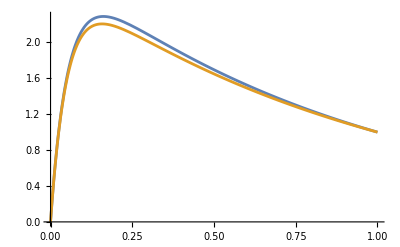

```mathematica
Plot[
{
	ysol/.ϵ->10^-1,
	yComp/.ϵ->10^-1
},
{x,0,1}
]
```

```mathematica
AsymptoticDSolveValue[
	{eq,y[0]==0,y[1]==1},
	y[x], x, {ϵ,0,1}
] == yComp // Simplify
```

True